```mathematica
xephotoion=Import["/Users/Max/ownCloud/Doktor/Thesis/calculations/xe.txt","Data"];
hephotoion=Import["/Users/Max/ownCloud/Doktor/Thesis/calculations/he.txt","Data"];
```

```mathematica
xephotoion//Dimensions
hephotoion//Dimensions
```

{186,2}

{105,2}

```mathematica
Needs["PlotLegends`"]
```

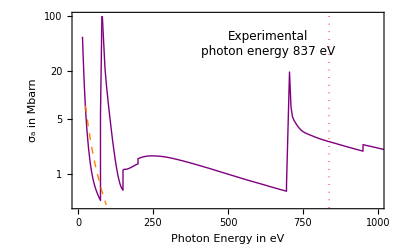

```mathematica
ListLogPlot[{xephotoion,hephotoion},Joined->True,PlotRange->{{0,1000},{0.4,100}},Frame->True,PlotStyle->{Directive[Thick,Purple],Directive[Thick,Dashed,Orange]},FrameLabel->{"Photon Energy in eV","σ_a in Mbarn"},Frame->True,FrameStyle->Directive[12],Epilog->{{Directive[Red, Thick, Dotted],Line[{{837,-1},{837.1,100}}]},{Text[Style["Experimental\nphoton energy 837 eV",FontSize->12,TextAlignment->Right],{635,3.8}]}}]
```